```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Mariusz\Desktop\graph_connectivity

```mathematica
LaunchKernels[]
```

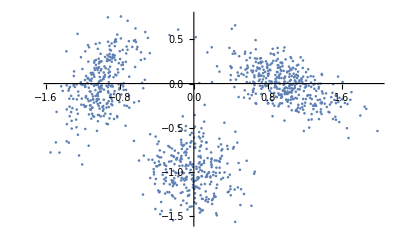

```mathematica
SeedRandom[2]
data=RandomVariate[MixtureDistribution[{0.3,0.4,0.3},{BinormalDistribution[{-1,0},{0.2,0.3},0.5],BinormalDistribution[{1,0},{0.3,0.2},-0.5],BinormalDistribution[{0,-1},{0.25,0.25},0]}],1000];
ListPlot@data
(* generate and plot some data *)
```

```mathematica
connClustering[points_,kNN_,d_,a_,save_:"no"]:=Module[{g,diam,DistMat,Vv,Gkvda,SI,singular,singIndices,clusters,len,color,commAssign,members,class,finalClassification,finalOutput,plotClusters,points1,points2,plot1,plot2},
g=NearestNeighborGraph[points,kNN];(* construct the kNN graph *)
diam=GraphDiameter[g];(* and its diameter *)

If[Not@(5≤d≤GraphDiameter@g&&a<2 d),"d or a out of bounds",(* check if the rules of thumb for d and a are satisfied *)
DistMat=GraphDistanceMatrix[g];(* the whole distance matrix is computed only once *)
Vv[graph_,v_,dd_]:=Flatten@Position[GraphDistanceMatrix[graph,dd][[v]],dd];(* definition of the set of distance-d vertices of point v *)
Gkvda[graph_,v_,dd_,aa_]:=With[{vat=Vv[g,v,dd]},Graph[vat,Select[{#[[1]]<->#[[2]],DistMat[[#[[1]],#[[2]]]]}&/@Select[DeleteDuplicates[Sort/@Flatten[Outer[List,vat,vat],1]],#[[1]]=!=#[[2]]&],#[[2]]<=a&][[All,1]]]
];(* definition of the G^k_v,d,a graph *)
SI[graph_,v_,dd_,aa_]:=Length@ConnectedGraphComponents@Gkvda[graph,v,dd,aa];(* singular index of point v *)

singular=ParallelMap[{#,SI[g,#,d,a]}&,Range[VertexCount@g]];(* list of vertices and their corresponding singular indices *)
singIndices=Select[singular,#[[2]]>1&][[All,1]];(* list of singular points and their corresponding singular indices *)
clusters=VertexDelete[IndexGraph@g,singIndices];(* graph with singular points removed *)
len=Length@ConnectedComponents@clusters;(* number of connected components; a helper quantity to make the further code more concise *)
color=Flatten@ConstantArray[{Green,Red,Blue,Yellow,Cyan,Orange,Magenta,Brown},Ceiling[len/8]];(* the colors on the plot will start to loop over if there are more than eight communities *)

commAssign=If[Length@ConnectedComponents[clusters]>1,If[#[[1]]==#[[2]],RandomInteger[{1,Length@#}],First@Ordering[#,1]]&/@(Map[Min,#,{2}]&@Outer[DistMat[[#1,#2]]&,singIndices,ConnectedComponents[clusters]]),ConstantArray[1,Length@singIndices]];(* assigns community membership of the singular points *)

(members=ConnectedComponents[clusters]~Join~(Pick[singIndices,commAssign,#]&/@Range[len]))/.{}->Nothing;
(* assigns membership within the clusters *)

class=Transpose[{Range[len]~Join~Range[len],ConstantArray[0,len]~Join~ConstantArray[1,len]}];
(* helper to format the final output; contains classes to be assigned to points: cluster memberships, and whether a point is singular (1) or not (0) *)

finalClassification=If[len>1,SortBy[Flatten[Table[{members[[i,j]]}~Join~class[[i]]~Join~{singular[[members[[i,j]],2]]},{i,1,Length@members},{j,1,Length@members[[i]]}],1],First],Transpose@{Range@Length@points,ConstantArray[1,Length@points],ReplacePart[ConstantArray[0,Length@points],Rule[#,1]&/@singIndices]}];(* the 1st column is the point number; the 2nd is the cluster membership; the 3rd is a flag indicating whether a point is singular or not; the 4th column is the SI *)

finalOutput={{"k","d","a","sing.points fraction"},{kNN,d,a,N@Length[singIndices]/Length[points]},{"there are "<>ToString[Max@finalClassification[[All,2]]]<>" communities and "<>ToString[Length@singIndices]<>" singular points"},{"point number","cluster number","singular point","SI"}}~Join~finalClassification;

points1=GatherBy[SortBy[#,Last]&@({points[[#[[1]]]],#[[2]]}&/@Select[finalOutput[[5;;]],#[[3]]==0&]),Last][[All,All,1]];
points2=GatherBy[SortBy[#,Last]&@({points[[#[[1]]]],#[[2]]}&/@Select[finalOutput[[5;;]],#[[3]]==1&]),Last][[All,All,1]];
plot1=ListPlot[points1,PlotStyle->color[[1;;len]],PlotMarkers->{"●",5}];
plot2=ListPlot[points2,PlotStyle->color[[1;;len]],PlotMarkers->{"★",7}];
plotClusters=Show[plot1,plot2,Frame->True,Axes->False,PlotRange->All,FrameStyle->Black,AspectRatio->1];
(* plots the clusters, highlighting singular points *)

If[save=="yes",
{Export[ToString[kNN]<>"_"<>ToString[d]<>"_"<>ToString[a]<>".txt",finalOutput,"Table"];
Export[ToString[kNN]<>"_"<>ToString[d]<>"_"<>ToString[a]<>".png",plotClusters];},Nothing];

{finalOutput,plotClusters}
(* the function returns a list of two elements: the 1st is the list of cluster memberships, flags indicating whether a point is singular or not, and the SI, with descriptive headers; 2nd is a plot displaying the results of the clustering *)
]
]
```

```mathematica
GraphDiameter@NearestNeighborGraph[data,6]
(* check for the maximal d *)
```

36

```mathematica
out=connClustering[data,6,5,7,"yes"];//AbsoluteTiming
```

{34.0654,Null}

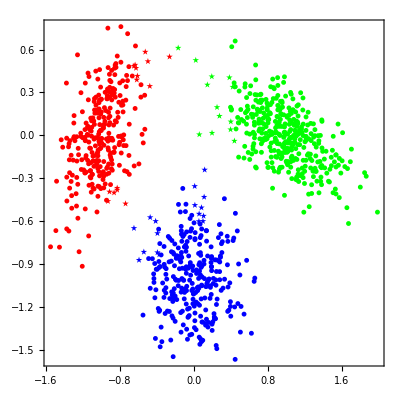

```mathematica
out[[2]]
```

```mathematica
(* from the output files *)
Module[{imp,len,color,points1,points2,plot1,plot2},
imp=Import["6_5_7.txt","Table"][[5;;]];
len=Max@imp[[All,2]];
color=Flatten@ConstantArray[{Green,Red,Blue,Yellow,Cyan,Orange,Magenta,Brown},Ceiling[len/8]];

points1=GatherBy[SortBy[#,Last]&@({data[[#[[1]]]],#[[2]]}&/@Select[imp,#[[3]]==0&]),Last][[All,All,1]];
points2=GatherBy[SortBy[#,Last]&@({data[[#[[1]]]],#[[2]]}&/@Select[imp,#[[3]]==1&]),Last][[All,All,1]];

plot1=ListPlot[points1,PlotStyle->color[[1;;len]],PlotMarkers->{"●",5}];
plot2=ListPlot[points2,PlotStyle->color[[1;;len]],PlotMarkers->{"★",7}];

Show[plot1,plot2,Frame->True,Axes->False,PlotRange->All,FrameStyle->Black,AspectRatio->1]
]
```

-Graphics-